```mathematica
UniPoint[u_,t_]:={Sqrt[1-u^2]Cos[t],Sqrt[1-u^2]Sin[t],u}
```

```mathematica
SeedRandom[621859188853648];

ZZZ[k_]:=Table[UniPoint[RandomReal[{-1,1}], RandomReal[{0,2Pi}]],{i,k}]
```

```mathematica
ZZ=Map[S2InftyDis[N[#]]&,Table[ZZZ[i],{i,60}]]
```

{1,0.751815,0.734101,0.652021,0.515728,0.4771,0.625143,0.48759,0.431639,0.412517,0.395593,0.346066,0.336833,0.314439,0.279437,0.30407,0.286362,0.424463,0.351539,0.377632,0.402771,0.410549,0.268436,0.257758,0.322154,0.230465,0.242971,0.288209,0.277945,0.285116,0.251934,0.25632,0.216692,0.273512,0.266147,0.227349,0.316238,0.222645,0.251078,0.245253,0.306414,0.193639,0.203898,0.189733,0.21006,0.249561,0.250166,0.239506,0.167911,0.227489,0.201662,0.225626,0.219257,0.304391,0.215003,0.172059,0.181774,0.187281,0.257755,0.209049}

```mathematica
Picture[ZZZ[10000]]
```

-Graphics3D-

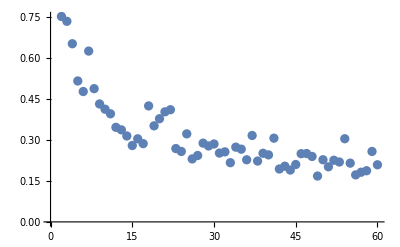

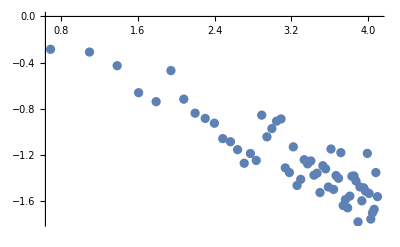

```mathematica
ListPlot[Drop[{Table[i,{i,60}],ZZ}//Transpose,1]]
ListPlot[Drop[Log[{Table[i,{i,60}],ZZ}]//Transpose,1]]
```

```mathematica
Fit[Drop[Log[{Table[i,{i,60}],ZZ}]//Transpose,1],{1,x},x]
```

0.0548572-0.402787 x